```mathematica
$Assumptions={n∈Integers}
```

{n∈ℤ}

```mathematica
boxcar[x_]:=UnitStep[x]-UnitStep[x-1];
Λ[x_]:=UnitTriangle[x];
```

### Metal Disc at Thermal Equilibrium

#### (1)

```mathematica
u21[r_,θ_]:=r*Sin[θ]
```

```mathematica
Plot3D[u21[Norm[{x, y}],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

-Graphics3D-

#### (2)

```mathematica
u22[r_,θ_]:=r*Sin[θ]-1/3 r^3Sin[3θ]+1/5 r^5Sin[5θ]
```

```mathematica
Plot3D[u22[Norm[{x, y}],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

-Graphics3D-

#### (3)

```mathematica
u23[r_,θ_]:=r*Sin[θ]+1/4 r^2Cos[2θ]+1/9 r^3Sin[3θ]+1/16 r^4Cos[4θ]
```

```mathematica
Plot3D[u23[Norm[{x, y}],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

-Graphics3D-

#### (4)

```mathematica
∫_0^(2Pi) (Sin[n θ])^2ⅆθ
```

π

```mathematica
∫_0^(2Pi) (Cos[n θ])^2ⅆθ
```

π

```mathematica
A024=∫_0^(2Pi) boxcar[0]ⅆθ
```

2 π

```mathematica
1/Pi Integrate[boxcar[Pi θ]Cos[n θ],{θ,0, 2Pi}]
```

Sin[n/π]/(n π)

```mathematica
An24[n_]:=Sin[n/π]/(n π)
```

```mathematica
1/Pi Integrate[boxcar[Pi θ]Sin[n θ],{θ,0, 2Pi}]
```

(1-Cos[n/π])/(n π)

```mathematica
Bn24[n_]:=(1-Cos[n/π])/(n π)
```

```mathematica
u24[R_,k_,r_,θ_]:=∑_(n=1)^k ((r/R)^n)(An24[n]Cos[n θ]+Bn24[n]Sin[n θ])+1/(2Pi^2)
```

```mathematica
Plot3D[u24[1,50,Sqrt[x^2+y^2],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,PlotRange->Full,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

-Graphics3D-

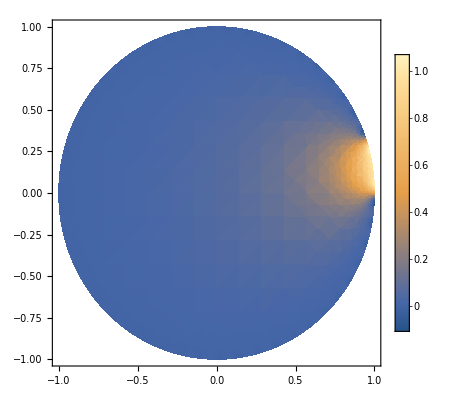

```mathematica
DensityPlot[u24[1,50,Sqrt[x^2+y^2],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,PlotRange->Full,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

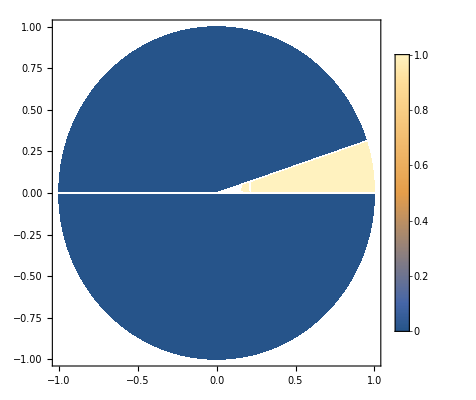

```mathematica
DensityPlot[boxcar[Pi ArcTan[x,y]],{x,-1,1},{y,-1,1},RegionFunction->Function[{x, y}, x^2 + y^2 ≤1],PlotLegends->Automatic]
```

#### (4)

```mathematica
∫_0^(2Pi) (Sin[n θ])^2ⅆθ
```

π

```mathematica
∫_0^(2Pi) (Cos[n θ])^2ⅆθ
```

π

```mathematica
A025=1/(2Pi)∫_-Pi^Pi Λ[0]ⅆθ
```

1

```mathematica
1/Pi Integrate[Λ[Pi θ]Cos[n θ],{θ,-Pi, Pi}]
```

-(2 (-π+π Cos[n/π]))/(n^2 π)

```mathematica
An25[n_]:=-(2 (-π+π Cos[n/π]))/(n^2 π)
```

```mathematica
Bn25[n_]:=0
```

```mathematica
u25[R_,k_,r_,θ_]:=∑_(n=1)^k ((r/R)^n)(An25[n]Cos[n θ])+1
```

```mathematica
Plot3D[u25[1,50,Sqrt[x^2+y^2],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,PlotRange->Full,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

-Graphics3D-

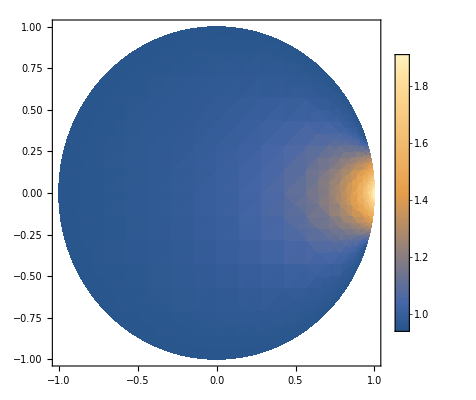

```mathematica
DensityPlot[u25[1,50,Sqrt[x^2+y^2],ArcTan[x,y]],{x,-1,1},{y,-1,1},PlotLegends->Automatic,Exclusions->None,PlotRange->Full,RegionFunction->Function[{x, y}, x^2 + y^2 ≤1]]
```

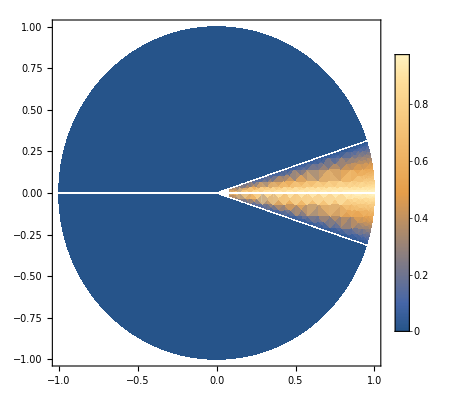

```mathematica
DensityPlot[Λ[Pi ArcTan[x,y]],{x,-1,1},{y,-1,1},RegionFunction->Function[{x, y}, x^2 + y^2 ≤1],PlotLegends->Automatic]
```

### The Piano String Revisited

#### (a) Find the most Discordant

```mathematica
α=0;β=0; c=10^2;
```

```mathematica
ω[n_,L_]:=(n Pi)/L Sqrt[1+α((n Pi)/L)^2]
```

```mathematica
η[n_,L_]:=c ω[n,L] √(1-β^2/(((2 c n Pi)/L)^2(1+α((n Pi)/L)^2)))
```

```mathematica
η1 = η[1,L]
```

(100 π)/L

```mathematica
b[δ_,x0_,n_,L_]:=(δ Sin[ω[n,L]x0])/η[n,L](Sin[δ ω[n,L]]/(δ ω[n,L])+(2Pi Cos[δ ω[n,L]])/(π^2-(2δ ω[n,L])))
```

```mathematica
concor[n_,L_]:=12Log[2, η[n,L]/η[1,L]]
```

```mathematica
Table[{i,N[concor[i,1]]},{i,1,16}]
```

{{1,0.},{2,12.},{3,19.0196},{4,24.},{5,27.8631},{6,31.0196},{7,33.6883},{8,36.},{9,38.0391},{10,39.8631},{11,41.5132},{12,43.0196},{13,44.4053},{14,45.6883},{15,46.8827},{16,48.}}

the 11th overtone is the most discordant

#### (b) Find Hammer parameters that minimize the energy in the discordant overtones

```mathematica
Table[{i,N[b[.1,.5,i,1]]},{i,1,16}]
```

{{1,0.000518927},{2,2.97366×10^-20},{3,-0.000140155},{4,-1.98956×10^-20},{5,0.0000405285},{6,3.62994×10^-21},{7,0.0000139654},{8,1.5899×10^-20},{9,-0.0000462791},{10,-3.41468×10^-20},{11,0.0000610438},{12,4.55648×10^-20},{13,-0.0000579978},{14,-3.94789×10^-20},{15,4.50316×10^-6},{16,2.09929×10^-19}}

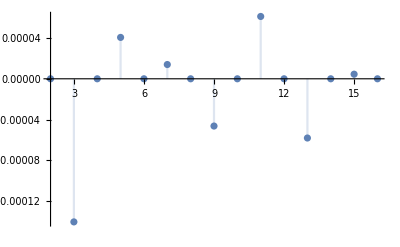

```mathematica
DiscretePlot[(b[.1,.5,i,1]),{i,2,16},PlotRange->Full]
```

```mathematica
NSolve[{b[δ,x0,2,1]==1/4,b[δ,x0,4,1]==1/16},{δ,x0}]
```

$Aborted

```mathematica
Pl
```

```mathematica
(b[δ,x0,7,1])^2+(b[δ,x0,11,1])^2+(b[δ,x0,13,1])^2
```

(δ^2 Sin[7 π x0]^2 ((2 π Cos[7 π δ])/(π^2-14 π δ)+Sin[7 π δ]/(7 π δ))^2)/(490000 π^2)+(δ^2 Sin[11 π x0]^2 ((2 π Cos[11 π δ])/(π^2-22 π δ)+Sin[11 π δ]/(11 π δ))^2)/(1210000 π^2)+(δ^2 Sin[13 π x0]^2 ((2 π Cos[13 π δ])/(π^2-26 π δ)+Sin[13 π δ]/(13 π δ))^2)/(1690000 π^2)

```mathematica
Simplify[%150]
```

1/(10020010000 π^2)δ^2 (20449 Sin[7 π x0]^2 ((2 Cos[7 π δ])/(π-14 δ)+Sin[7 π δ]/(7 π δ))^2+8281 Sin[11 π x0]^2 ((2 Cos[11 π δ])/(π-22 δ)+Sin[11 π δ]/(11 π δ))^2+5929 Sin[13 π x0]^2 ((2 Cos[13 π δ])/(π-26 δ)+Sin[13 π δ]/(13 π δ))^2)

```mathematica
NMinimize[{%151,0≤x0≤1&& 0≤ δ≤x0},{x0,δ}]
```

{8.75224×10^-12,{x0→0.144805,δ→0.0567053}}

```mathematica
Table[{i,N[b[0.05670530907460242,0.14480457808512992,i,1]]},{i,1,16}]
```

{{1,0.000130442},{2,0.000115559},{3,0.0000923131},{4,0.0000647492},{5,0.0000374696},{6,0.0000145931},{7,-1.13849×10^-6},{8,-8.87796×10^-6},{9,-9.68782×10^-6},{10,-6.0663×10^-6},{11,-1.1307×10^-6},{12,2.30315×10^-6},{13,2.48548×10^-6},{14,-8.65466×10^-7},{15,-6.61986×10^-6},{16,-0.0000127108}}

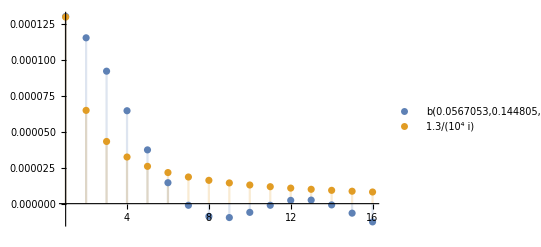

```mathematica
DiscretePlot[{b[0.05670530907460242,0.14480457808512992,i,1],1.3/(10^4i)},{i,1,16},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Manipulate[DiscretePlot[{Abs[b[δ,x0,i,1]],2.6/(10^4i^2)},{i,1,16},PlotRange->Full],{δ,0.04,0.07},{x0,0,1}]
```

#### (c) What changes when the piano wire has significant bending stiffness?

```mathematica
α=0.1;β=0; c=10^2;
```

```mathematica
Table[{i,N[concor[i,1]]},{i,1,16}]
```

{{1,0.},{2,19.8974},{3,32.9056},{4,42.4745},{5,50.0132},{6,56.2224},{7,61.4967},{8,66.079},{9,70.1288},{10,73.7565},{11,77.0415},{12,80.0428},{13,82.8053},{14,85.3642},{15,87.7473},{16,89.9772}}

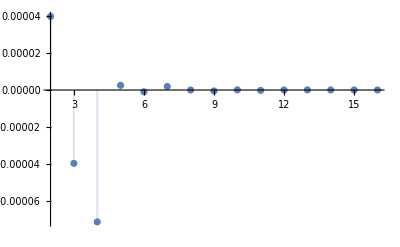

```mathematica
DiscretePlot[(b[.1,.5,i,1]),{i,2,16},PlotRange->Full]
```

```mathematica
α=1;β=0; c=10^2;
```

```mathematica
Table[{i,N[concor[i,1]]},{i,1,16}]
```

{{1,0.},{2,23.3811},{3,37.3006},{4,47.2192},{5,54.9259},{6,61.228},{7,66.559},{8,71.1783},{9,75.2536},{10,78.8996},{11,82.1982},{12,85.2098},{13,87.9803},{14,90.5456},{15,92.9339},{16,95.168}}

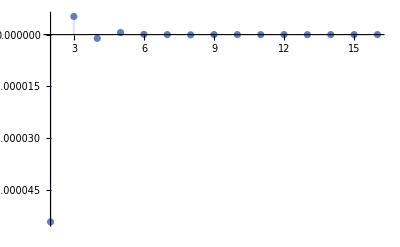

```mathematica
DiscretePlot[(b[.1,.5,i,1]),{i,2,16},PlotRange->Full]
```

```mathematica
α=10;β=0; c=10^2;
```

```mathematica
Table[{i,N[concor[i,1]]},{i,1,16}]
```

{{1,0.},{2,23.9346},{3,37.9616},{4,47.9182},{5,55.6425},{6,61.9543},{7,67.291},{8,71.9141},{9,75.992},{10,79.6399},{11,82.9398},{12,85.9524},{13,88.7238},{14,91.2897},{15,93.6785},{16,95.9131}}

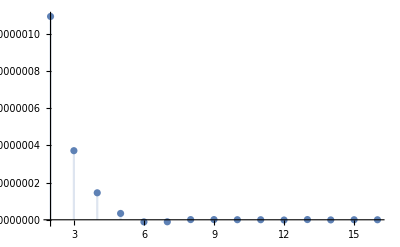

```mathematica
DiscretePlot[(b[.1,.5,i,1]),{i,2,16},PlotRange->Full]
```

With a significant bending stiffness, the PDE now starts to have a beam-equation behavior in addition to a standard wave-equation behavior. The perfectly concordant overtone at 2^n now disappears, and every overtone is somewhat discordant.

#### (2) Music Box

```mathematica
Solve[k^4-k^2-(δ/s)^2==0,k]
```

{{k→-(√(1-(√(s^2+4 δ^2))/s))/(√2)},{k→(√(1-(√(s^2+4 δ^2))/s))/(√2)},{k→-(√(1+(√(s^2+4 δ^2))/s))/(√2)},{k→(√(1+(√(s^2+4 δ^2))/s))/(√2)}}